# Fourier series

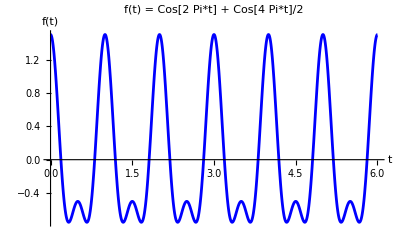

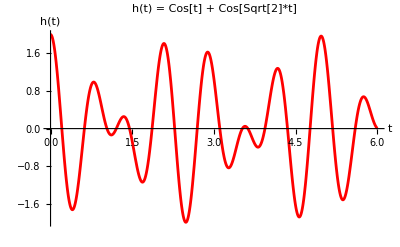

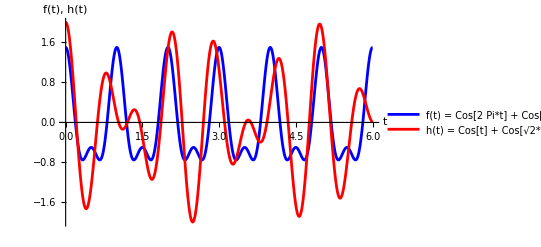

```mathematica
f[t_]:=Cos[2 Pi*t]+Cos[4 Pi*t]/2
h[t_]:=Cos[2Pi *t]+Cos[2Pi *√2*t]
Plot[f[t],{t,0,6},PlotLabel->"f(t) = Cos[2 Pi*t] + Cos[4 Pi*t]/2",AxesLabel->{"t","f(t)"},PlotStyle->Blue,PlotRange->All]

Plot[h[t],{t,0,6},PlotLabel->"h(t) = Cos[t] + Cos[Sqrt[2]*t]",AxesLabel->{"t","h(t)"},PlotStyle->Red,PlotRange->All]

Plot[{f[t],h[t]},{t,0,6},PlotLegends->{"f(t) = Cos[2 Pi*t] + Cos[4 Pi*t]/2","h(t) = Cos[t] + Cos[√2*t]"},PlotStyle->{Blue,Red},AxesLabel->{"t","f(t), h(t)"},PlotRange->All]
```

## Superposition of harmonic functions

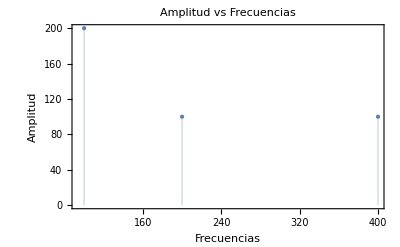

```mathematica
amplitudes={200,100,100};
frecuencias={100,200,400};

ListPlot[Transpose[{frecuencias,amplitudes}],Filling->Axis,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"Frecuencias","Amplitud"},PlotLabel->"Amplitud vs Frecuencias"]
```

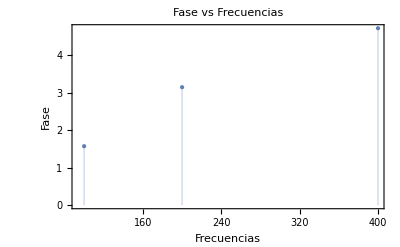

```mathematica
fases={Pi/2,Pi,3 Pi/2};

ListPlot[Transpose[{frecuencias,fases}],Filling->Axis,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"Frecuencias","Fase"},PlotLabel->"Fase vs Frecuencias"]
```

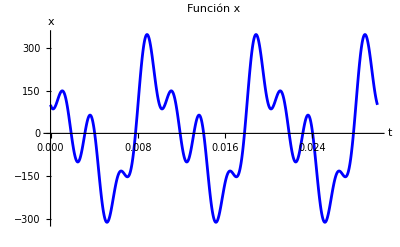

```mathematica
x[t_]:=200 Sin[2 Pi*100*t+Pi/2]+100 Sin[2 Pi*200*t+Pi]+100 Sin[2 Pi*400*t+3 Pi/2]

Plot[x[t],{t,0,0.03},PlotLabel->"Función x",AxesLabel->{"t","x"},PlotStyle->Blue,PlotRange->All]
```

## Serie de Fourier Función Par

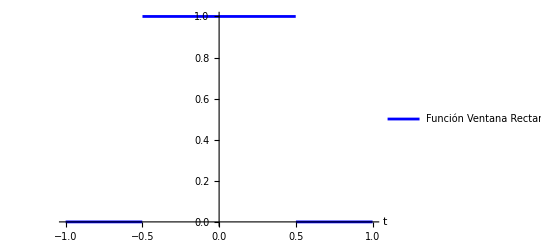

```mathematica
x[t_]:=Piecewise[{{DirichletWindow[t],-0.5<t<0.5}}]
Plot[{x[t]},{t,-1,1},PlotStyle->{Blue},PlotLegends->{"Función Ventana Rectangular"},AxesLabel->{"t"},PlotRange->All]
```

```mathematica
y[t_]=FullSimplify[FourierSeries[x[t],t,30]]
```

0.159155+0.305212 Cos[t]+0.267849 Cos[2 t]+0.211675 Cos[3 t]+0.144719 Cos[4 t]+0.0761998 Cos[5 t]+0.0149733 Cos[6 t]-0.0319022 Cos[7 t]-0.0602244 Cos[8 t]-0.0691461 Cos[9 t]-0.061047 Cos[10 t]-0.0408328 Cos[11 t]-0.0148235 Cos[12 t]+0.0105346 Cos[13 t]+0.029875 Cos[14 t]+0.03981 Cos[15 t]+0.0393653 Cos[16 t]+0.0299019 Cos[17 t]+0.0145757 Cos[18 t]-0.00251804 Cos[19 t]-0.0173167 Cos[20 t]-0.0266682 Cos[21 t]-0.028937 Cos[22 t]-0.0242317 Cos[23 t]-0.014233 Cos[24 t]-0.00168887 Cos[25 t]+0.0102879 Cos[26 t]+0.018952 Cos[27 t]+0.0225229 Cos[28 t]+0.0205232 Cos[29 t]+0.0137995 Cos[30 t]

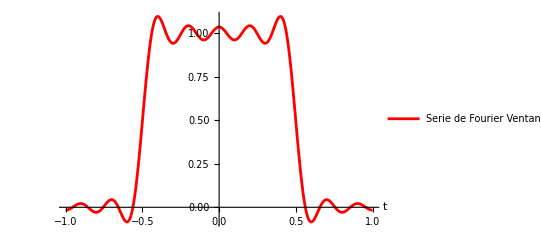

```mathematica
Plot[{y[t]},{t,-1,1},PlotStyle->{Red},PlotLegends->{"Serie de Fourier Ventana Rectangular"},AxesLabel->{"t"},PlotRange->All]
```

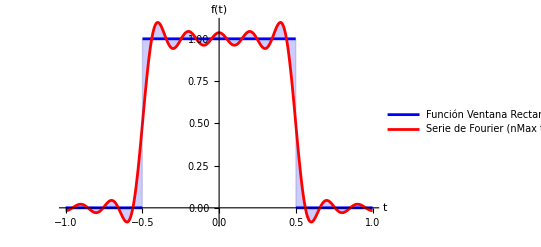

```mathematica
Plot[{x[t],y[t]},{t,-1,1},PlotStyle->{Blue,Red},PlotLegends->{"Función Ventana Rectangular","Serie de Fourier (nMax términos)"},Filling->{1->{2}},AxesLabel->{"t","f(t)"},PlotRange->All]
```

## Fourier Series Odd Function

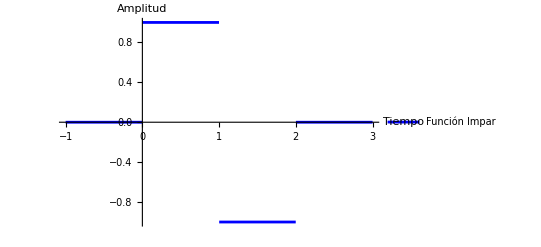

```mathematica
x[t_]:=Piecewise[{{HeavisideTheta[t+1],0<t<1}}]+Piecewise[{{-1*HeavisideTheta[t-1],1<t<2}}]+Piecewise[{{0,0<t},{0,t>2}}];
Plot[{x[t]},{t,-1,3},PlotLegends->{"Función Impar"},PlotStyle->{Blue},AxesLabel->{"Tiempo","Amplitud"},PlotRange->Full]
```

```mathematica
y[t_]=FullSimplify[FourierSeries[x[t],t,30]]
```

-(ⅈ (-1+ⅇ^ⅈ)^2 ⅇ^(ⅈ (-2+t)))/(2 π)-(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(3 ⅈ (-2+t)))/(6 π)-(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(4 ⅈ (-2+t)))/(8 π)-(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(5 ⅈ (-2+t)))/(10 π)-(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(7 ⅈ (-2+t)))/(14 π)-(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(9 ⅈ (-2+t)))/(18 π)-(ⅈ (-1+ⅇ^(11 ⅈ))^2 ⅇ^(11 ⅈ (-2+t)))/(22 π)-(ⅈ (-1+ⅇ^(13 ⅈ))^2 ⅇ^(13 ⅈ (-2+t)))/(26 π)-(ⅈ (-1+ⅇ^(15 ⅈ))^2 ⅇ^(15 ⅈ (-2+t)))/(30 π)-(ⅈ (-1+ⅇ^(17 ⅈ))^2 ⅇ^(17 ⅈ (-2+t)))/(34 π)-(ⅈ (-1+ⅇ^(19 ⅈ))^2 ⅇ^(19 ⅈ (-2+t)))/(38 π)-(ⅈ (-1+ⅇ^(20 ⅈ))^2 ⅇ^(20 ⅈ (-2+t)))/(40 π)-(ⅈ (-1+ⅇ^(21 ⅈ))^2 ⅇ^(21 ⅈ (-2+t)))/(42 π)-(ⅈ (-1+ⅇ^(22 ⅈ))^2 ⅇ^(22 ⅈ (-2+t)))/(44 π)-(ⅈ (-1+ⅇ^(23 ⅈ))^2 ⅇ^(23 ⅈ (-2+t)))/(46 π)-(ⅈ (-1+ⅇ^(24 ⅈ))^2 ⅇ^(24 ⅈ (-2+t)))/(48 π)-(ⅈ (-1+ⅇ^(25 ⅈ))^2 ⅇ^(25 ⅈ (-2+t)))/(50 π)-(ⅈ (-1+ⅇ^(26 ⅈ))^2 ⅇ^(26 ⅈ (-2+t)))/(52 π)-(ⅈ (-1+ⅇ^(27 ⅈ))^2 ⅇ^(27 ⅈ (-2+t)))/(54 π)-(ⅈ (-1+ⅇ^(28 ⅈ))^2 ⅇ^(28 ⅈ (-2+t)))/(56 π)-(ⅈ (-1+ⅇ^(29 ⅈ))^2 ⅇ^(29 ⅈ (-2+t)))/(58 π)-(ⅈ (-1+ⅇ^(30 ⅈ))^2 ⅇ^(30 ⅈ (-2+t)))/(60 π)+(ⅈ (-1+ⅇ^ⅈ)^2 ⅇ^(-ⅈ t))/(2 π)+(ⅈ (-1+ⅇ^(2 ⅈ))^2 ⅇ^(-2 ⅈ t))/(4 π)+(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ t))/(6 π)+(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ t))/(8 π)+(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ t))/(10 π)+(ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ t))/(12 π)+(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ t))/(14 π)+(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ t))/(16 π)+(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ t))/(18 π)+(ⅈ (-1+ⅇ^(10 ⅈ))^2 ⅇ^(-10 ⅈ t))/(20 π)+(ⅈ (-1+ⅇ^(11 ⅈ))^2 ⅇ^(-11 ⅈ t))/(22 π)+(ⅈ (-1+ⅇ^(12 ⅈ))^2 ⅇ^(-12 ⅈ t))/(24 π)+(ⅈ (-1+ⅇ^(13 ⅈ))^2 ⅇ^(-13 ⅈ t))/(26 π)+(ⅈ (-1+ⅇ^(14 ⅈ))^2 ⅇ^(-14 ⅈ t))/(28 π)+(ⅈ (-1+ⅇ^(15 ⅈ))^2 ⅇ^(-15 ⅈ t))/(30 π)+(ⅈ (-1+ⅇ^(16 ⅈ))^2 ⅇ^(-16 ⅈ t))/(32 π)+(ⅈ (-1+ⅇ^(17 ⅈ))^2 ⅇ^(-17 ⅈ t))/(34 π)+(ⅈ (-1+ⅇ^(18 ⅈ))^2 ⅇ^(-18 ⅈ t))/(36 π)+(ⅈ (-1+ⅇ^(19 ⅈ))^2 ⅇ^(-19 ⅈ t))/(38 π)+(ⅈ (-1+ⅇ^(20 ⅈ))^2 ⅇ^(-20 ⅈ t))/(40 π)+(ⅈ (-1+ⅇ^(21 ⅈ))^2 ⅇ^(-21 ⅈ t))/(42 π)+(ⅈ (-1+ⅇ^(22 ⅈ))^2 ⅇ^(-22 ⅈ t))/(44 π)+(ⅈ (-1+ⅇ^(23 ⅈ))^2 ⅇ^(-23 ⅈ t))/(46 π)+(ⅈ (-1+ⅇ^(24 ⅈ))^2 ⅇ^(-24 ⅈ t))/(48 π)+(ⅈ (-1+ⅇ^(25 ⅈ))^2 ⅇ^(-25 ⅈ t))/(50 π)+(ⅈ (-1+ⅇ^(26 ⅈ))^2 ⅇ^(-26 ⅈ t))/(52 π)+(ⅈ (-1+ⅇ^(27 ⅈ))^2 ⅇ^(-27 ⅈ t))/(54 π)+(ⅈ (-1+ⅇ^(28 ⅈ))^2 ⅇ^(-28 ⅈ t))/(56 π)+(ⅈ (-1+ⅇ^(29 ⅈ))^2 ⅇ^(-29 ⅈ t))/(58 π)+(ⅈ (-1+ⅇ^(30 ⅈ))^2 ⅇ^(-30 ⅈ t))/(60 π)+(ⅈ ⅇ^(2 ⅈ (-1+t)) Sin[1]^2)/π+(ⅈ ⅇ^(6 ⅈ (-1+t)) Sin[3]^2)/(3 π)+(ⅈ ⅇ^(8 ⅈ (-1+t)) Sin[4]^2)/(4 π)+((-1+ⅇ^(10 ⅈ)) ⅇ^(5 ⅈ (-3+2 t)) Sin[5])/(10 π)+((-1+ⅇ^(12 ⅈ)) ⅇ^(6 ⅈ (-3+2 t)) Sin[6])/(12 π)+((-1+ⅇ^(14 ⅈ)) ⅇ^(7 ⅈ (-3+2 t)) Sin[7])/(14 π)+((-1+ⅇ^(16 ⅈ)) ⅇ^(8 ⅈ (-3+2 t)) Sin[8])/(16 π)+((-1+ⅇ^(18 ⅈ)) ⅇ^(9 ⅈ (-3+2 t)) Sin[9])/(18 π)

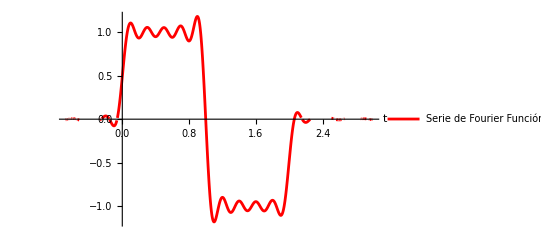

```mathematica
Plot[{y[t]},{t,-1,3},PlotStyle->{Red},PlotLegends->{"Serie de Fourier Función Impar"},AxesLabel->{"t"},PlotRange->All]
```

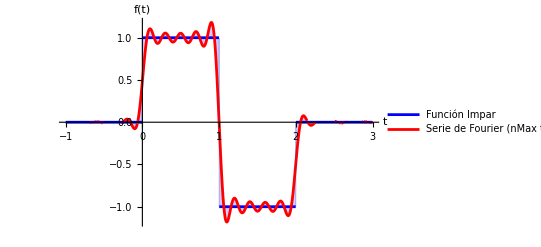

```mathematica
Plot[{x[t],y[t]},{t,-1,3},PlotStyle->{Blue,Red},PlotLegends->{"Función Impar","Serie de Fourier (nMax términos)"},Filling->{1->{2}},AxesLabel->{"t","f(t)"},PlotRange->All]
```